```mathematica
Qualau[a_,b_,d_,f_]:=
(******  S O L V E  S Y S T E M   
       A x = f ,
       [d_1 b_1  0  0   . . .  0        0       0   ]  
    [a_1 d_2 b_2 0   . . .  0        0       0   ]
A =  [. . . . . . . . . . . . . . . . . . . . . . ],
       [0    0   0  0 . . . a_{n-1} d_{n-1} b_{n-1} ]
    [0    0   0  0 . . .     0       a_n     d_n  ]
f = [f_1 f_2 . . . f_n]^T 
*******)
Module[
{i,alpha,beta,sheshim,n},
n=Length[d];
alpha=Table[0,{i,n+1}];
beta=Table[0,{i,n+1}];
sheshim=Table[0,{i,n}];
alpha[[2]]=-b[[1]]/d[[1]]//N;
beta[[2]]=f[[1]]/d[[1]]//N;
For[i=2,i≤n,i++,
If[i<n,
alpha[[i+1]]=-b[[i]]/(a[[i-1]]*alpha[[i]]+d[[i]])//N;
];
beta[[i+1]]=(f[[i]]-beta[[i]]*a[[i-1]])/(a[[i-1]]*alpha[[i]]+d[[i]])//N
];
sheshim[[n]]=beta[[n+1]];
For[i=n-1,i>0,i--,
sheshim[[i]]=alpha[[i+1]]*sheshim[[i+1]]+beta[[i+1]]//N;
];
Return[sheshim]
]
```

```mathematica
CubicSpline[x_,y_,z_]:=(*S_i(x)=a_i+b_i(x-x_i)+c_i(x-x_i)^2/2+d_i(x-x_i)^3/6, x in (x_{i-1},x_i), i = 1, 2, ..., n
Return S_i(z), z in [x_{i-1}, x_i]*)
Module[
{a,b,c,d,f,i,n,h,s},
n=Length[x];
h=Table[0,{i,1,n}];
a=Table[1,{i,1,n}];
b=Table[1,{i,1,n}];
c=Table[0,{i,1,n}];
d=Table[1,{i,1,n}];
f=Table[0,{i,1,n}];
For[i=2,i<=n,i++,
h[[i]]=x[[i]]-x[[i-1]];
];
For[i=2,i<n,i++,
a[[i]]=h[[i]];
b[[i]]=h[[i+1]];
d[[i]]=2*(h[[i]]+h[[i+1]]);
f[[i]]=6 *((y[[i+1]]-y[[i]])/h[[i+1]]-(y[[i]]-y[[i-1]])/h[[i]]);
];
c=Qualau[a,b,d,f];
For[i=2,i≤n,i++,
d[[i]]=(c[[i]]-c[[i-1]])/h[[i]];
b[[i]]=h[[i]]c[[i]]/2-h[[i]]^2 d[[i]]/6+(y[[i]]-y[[i-1]])/h[[i]];
];
For[i=1,i<n,i++,
If[x[[i]]<=z &&z<x[[i+1]],
Break[]
];
];
i++;
s=y[[i]]+b[[i]] (z-x[[i]])+c[[i]] (z-x[[i]])^2/2+d[[i]] (z-x[[i]])^3/6;
Return[s]
]
```

```mathematica
(****Function *****)
```

```mathematica
testfunc[x_]:= 1/Sqrt[x];
h=2;n=8;
x=Table[1.1+(i-1) h,{i,1,n}]
y=Table[testfunc[x[[i]]]//N,{i,1,n}]
```

{3,5,7,9,11,13,15,17}

{0.57735,0.447214,0.377964,0.333333,0.301511,0.27735,0.258199,0.242536}

```mathematica
CubicSplineView[x_,y_]:=Module[
(*S_i(x)=a_i+b_i(x-x_i)+c_i(x-x_i)^2/2+d_i(x-x_i)^3/6, x in (x_{i-1},x_i), i = 1, 2, ..., n
Return arrays of coefficients a, b, c, d*)
{a,b,c,d,f,i,n,h},
n=Length[x];
h=Table[0,{i,1,n}];
a=Table[0,{i,1,n}];
b=Table[0,{i,1,n}];
c=Table[0,{i,1,n}];
d=Table[1,{i,1,n}];
f=Table[0,{i,1,n}];
For[i=2,i<=n,i++,
h[[i]]=x[[i]]-x[[i-1]];
];
For[i=2,i<n,i++,
a[[i]]=h[[i]];
b[[i]]=h[[i+1]];
d[[i]]=2*(h[[i]]+h[[i+1]]);
f[[i]]=6 *((y[[i+1]]-y[[i]])/h[[i+1]]-(y[[i]]-y[[i-1]])/h[[i]]);
];
c=Qualau[a,b,d,f];
For[i=2,i≤n,i++,
d[[i]]=(c[[i]]-c[[i-1]])/h[[i]];
b[[i]]=h[[i]]c[[i]]/2-h[[i]]^2 d[[i]]/6+(y[[i]]-y[[i-1]])/h[[i]];

];

Return[List[y,b,c,d]];
]
```

```mathematica
CubicSplineView[x,y]
```

{{0.91909,0.89207,0.87333,0.8625,0.85293,0.86324},{0,-0.477258,-0.264598,-0.238549,-0.00520572,0.303772},{0.,3.78854,4.71783,-3.67585,13.0096,-0.650479},{1,75.7709,18.5857,-167.874,333.709,-273.201}}

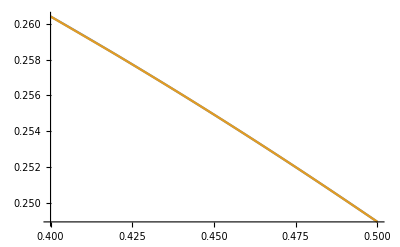

```mathematica
Plot[{testfunc[s],CubicSpline[x,y,s]},{s,x[[1]],x[[n]]}]
```

```mathematica
x={1.1,1.15,1.2,1.25,1.3,1.35};
y={0.91909,0.89207,0.87333,0.8625,0.85293,0.86324};
```